# machine learning

## 4pm — lions, tigers, and bears

```mathematica
Get["lions.mx"];
Get["tigers.mx"];
Get["bears.mx"];
```

```mathematica
RandomSample[lions,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[tigers,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomSample[bears,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length/@{lions,tigers,bears}
```

{800,800,800}

```mathematica
data=RandomSample@Flatten[{
Map[#->"lion"&,lions],
Map[#->"tiger"&,tigers],
Map[#->"bear"&,bears]
}];
```

```mathematica
Take[data,10]
```

{-Graphics-→tiger,-Graphics-→tiger,-Graphics-→tiger,-Graphics-→lion,-Graphics-→tiger,-Graphics-→lion,-Graphics-→bear,-Graphics-→lion,-Graphics-→bear,-Graphics-→bear}

```mathematica
training=Take[data,2200];
validation=Take[data,-200];
```

```mathematica
RandomSample[training,5]
```

{-Graphics-→lion,-Graphics-→tiger,-Graphics-→lion,-Graphics-→tiger,-Graphics-→tiger}

```mathematica
RandomSample[validation,5]
```

{-Graphics-→lion,-Graphics-→lion,-Graphics-→tiger,-Graphics-→tiger,-Graphics-→lion}

```mathematica
net=NetGraph[<|
"convolve"->ConvolutionLayer[20,5],
"ramp"->ElementwiseLayer[Ramp],
"pool"->PoolingLayer[3,3],
"flatten"->FlattenLayer[],
"connect"->DotPlusLayer[3],
"softmax"->SoftmaxLayer[]
|>,
{"convolve"->"ramp"->"pool"->"flatten"->"connect"->"softmax"},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"lion","tiger","bear"}}]
]
```

NetGraph[]

```mathematica
result=NetTrain[net,training,ValidationSet->validation,TargetDevice->"GPU",MaxTrainingRounds->400]
```

NetGraph[]

```mathematica
sample=RandomSample[validation,10]
```

{-Graphics-→lion,-Graphics-→lion,-Graphics-→lion,-Graphics-→bear,-Graphics-→bear,-Graphics-→tiger,-Graphics-→bear,-Graphics-→bear,-Graphics-→bear,-Graphics-→lion}

```mathematica
result[-Graphics-]
```

lion

```mathematica
Table[{First[s],Last[s],result[First[s]]},{s,RandomSample[validation,10]}]//Grid
```

-Graphics- | bear | bear
-Graphics- | tiger | tiger
-Graphics- | bear | bear
-Graphics- | bear | bear
-Graphics- | lion | lion
-Graphics- | lion | lion
-Graphics- | lion | lion
-Graphics- | tiger | lion
-Graphics- | tiger | tiger
-Graphics- | bear | bear

```mathematica
cm=ClassifierMeasurements[result,validation]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.725

```mathematica
cm["Accuracy"]
```

0.68

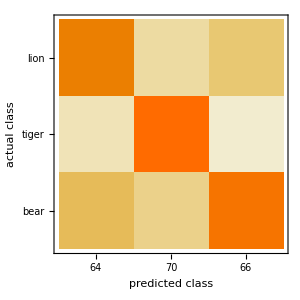

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
N[(51+60+57)/200]
```

0.84

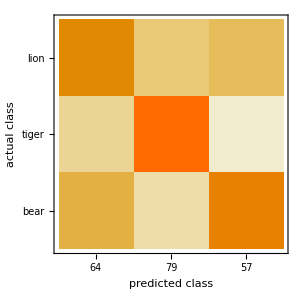

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
result
```

NetGraph[]

```mathematica
conv=NetExtract[result,1]
```

None

```mathematica
RandomSample[validation,3]
```

{-Graphics-→tiger,-Graphics-→bear,-Graphics-→tiger}

```mathematica
Image[Rescale/@conv[NetEncoder[{"Image",{100,100}}][-Graphics-]],Interleaving->False]
```

-Graphics-

```mathematica
Image/@Rescale/@conv[NetEncoder[{"Image",{100,100}}][-Graphics-]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Image[Rescale/@NetExtract[result,1][NetEncoder[{"Image",{100,100}}][-Graphics-]],Interleaving->False]
```

-Graphics-

```mathematica
Dataset[Table[<|"image"->First[s],"actual"->Last[s],"prediction"->result[First[s]],"probability"->result[First[s],"Probabilities"]|>,{s,validation}]]
```

Dataset[<>]